## 用最短tour寻找最短超级排列

#### 长度为3

```mathematica
len=3
f[0]=len;
```

3

```mathematica
per=StringJoin/@Permutations[ToString/@Range[len]]
```

{123,132,213,231,312,321}

```mathematica
f[x_]/;x!=0:=x
dis[a_,b_]:=Block[{n=1,x,y},x=ToExpression@Characters[b];y=ToExpression@Characters[a];While[Take[x,n]!=Take[y,-n]&&n<len,n++];f[len-n]](*n个元素的全排列构成一个集合S，计算S中任意两个元素之间的距离，找到一个遍历所有元素的最短路线，就找到了一个最小超级排列*)
```

```mathematica
{slen,tour}=FindShortestTour[per,DistanceFunction->dis]
st=Drop[per[[tour]],-1]
```

{12,{1,6,2,3,5,4,1}}

{123,321,132,213,312,231}

```mathematica
FindShortestTour[{"123","132","213","231","312","321"}]
```

{12,{1,2,6,5,3,4,1}}

```mathematica
s1={"123","231","312","213","132","321"};(*len=3的真正的最优解*)
```

```mathematica
tourlen[t_]:=(dis@@@Partition[t,2,1]//Total)+len
```

```mathematica
tourlen/@{per,st,s1}
```

{15,13,9}

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]]//Column
```

(123→321)→2
(321→132)→2
(132→213)→2
(213→312)→2
(312→231)→2
(231→123)→2

{1,4,5,3,2,6,1}

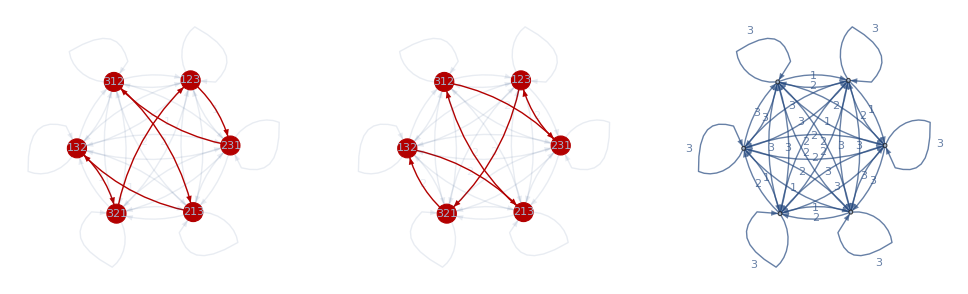

```mathematica
stour3=Flatten@(Position[per,#]&/@(s1~Join~{"123"}))
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]],VertexSize-> .25,VertexLabels->Table[stour3[[i]]->Placed[per[[stour3]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[stour3,2,1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]]]],
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

#### 长度为4

```mathematica
len=4
f[0]=len;
```

4

```mathematica
per=StringJoin/@Permutations[ToString/@Range[len]]
```

{1234,1243,1324,1342,1423,1432,2134,2143,2314,2341,2413,2431,3124,3142,3214,3241,3412,3421,4123,4132,4213,4231,4312,4321}

```mathematica
f[x_]/;x!=0:=x
dis[a_,b_]:=Block[{n=1,x,y},x=ToExpression@Characters[b];y=ToExpression@Characters[a];While[Take[x,n]!=Take[y,-n]&&n<len,n++];f[len-n]]
```

```mathematica
{slen,tour}=FindShortestTour[per,DistanceFunction->dis]
st=per[[Drop[%[[2]],-1]]]
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

{1234,3421,1342,4213,3142,2314,1423,4231,3214,1432,4321,2143,4312,1243,2431,3124,2134,3412,4123,3241,1324,2413,4132,2341}

```mathematica
tourlen[t_]:=(dis@@@Partition[t,2,1]//Total)+len
```

```mathematica
tourlen/@{per,st}
```

{93,55}

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]]//Column
```

(1234→3421)→2
(3421→1342)→3
(1342→4213)→2
(4213→3142)→3
(3142→2314)→3
(2314→1423)→2
(1423→4231)→1
(4231→3214)→4
(3214→1432)→2
(1432→4321)→1
(4321→2143)→2
(2143→4312)→2
(4312→1243)→2
(1243→2431)→1
(2431→3124)→2
(3124→2134)→4
(2134→3412)→2
(3412→4123)→1
(4123→3241)→3
(3241→1324)→3
(1324→2413)→2
(2413→4132)→1
(4132→2341)→3
(2341→1234)→3

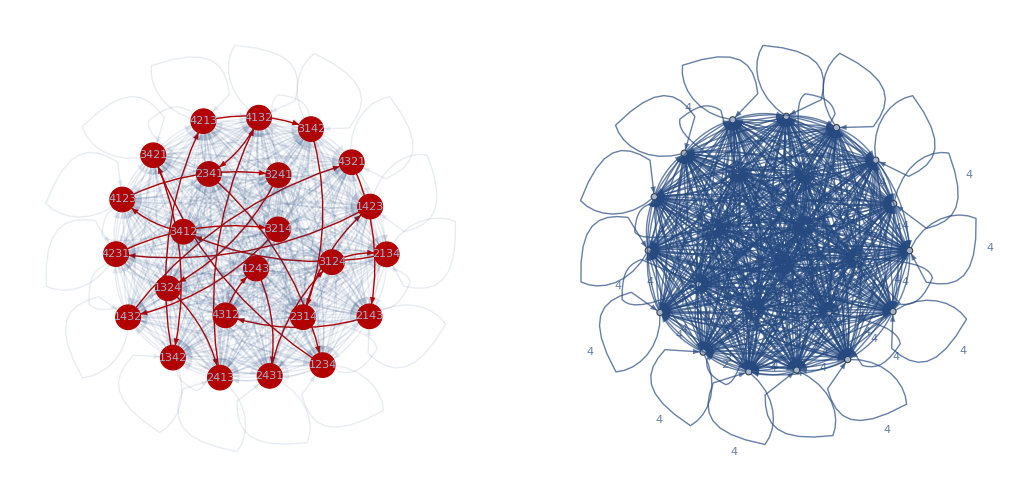

```mathematica
{slen,tour}=FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)];(*等价写法*)
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .55,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

## 内置算法找不到最短的路径(?)

### 4阶

{15,{1,2,3,4,1}}

{15,{1,2,3,4,1}}

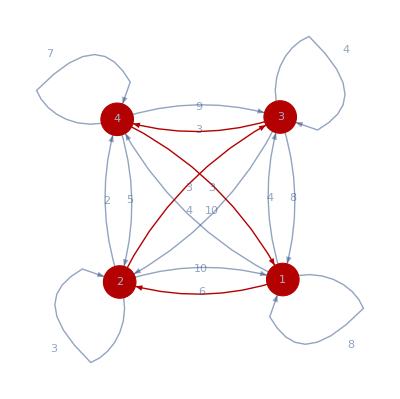

-Graphics-

```mathematica
d=RandomInteger[{1,10},{4,4}];
{len,tour}=FindShortestTour[{1,2,3,4},DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[3]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 5阶

{20,{1,5,4,2,3,1}}

{20,{1,5,4,2,3,1}}

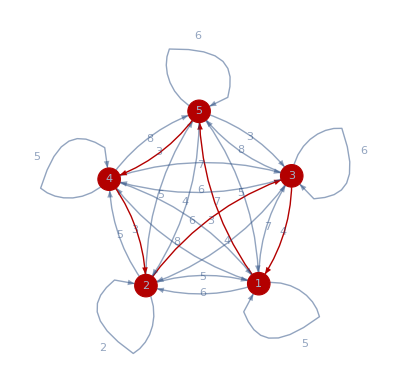

-Graphics-

```mathematica
n=5;d=RandomInteger[{1,8},{n,n}];
{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 6阶

{21,{1,3,4,5,6,2,1}}

{7,{1,5,2,6,4,3,1}}

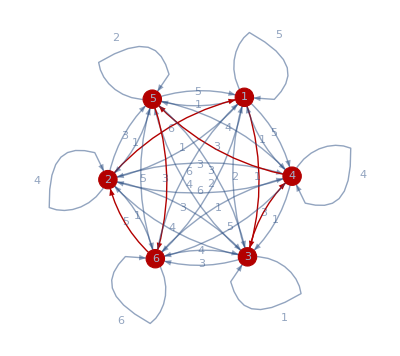

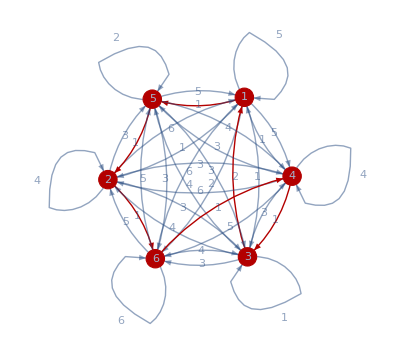

```mathematica
n=6;d=RandomInteger[{1,6},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 7阶

{254,{1,7,4,6,3,5,2,1}}

{113,{1,2,6,3,5,4,7,1}}

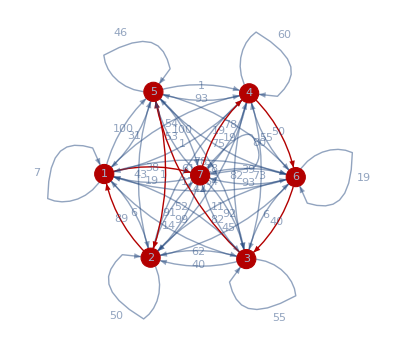

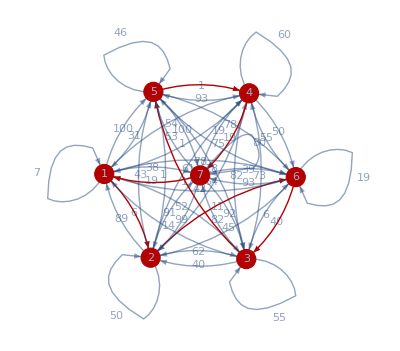

```mathematica
n=7;d=RandomInteger[{1,100},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 8阶

{259,{1,3,4,5,7,2,8,6,1}}

{177,{1,6,7,2,8,3,5,4,1}}

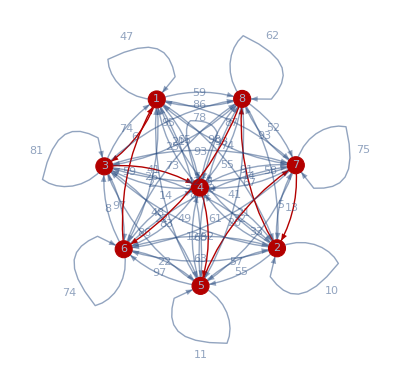

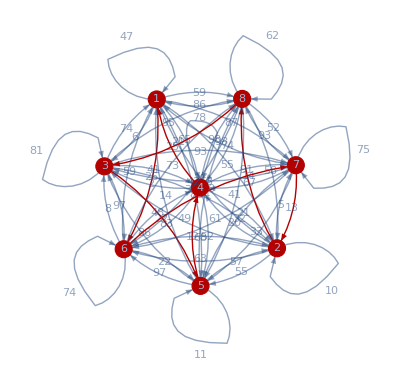

```mathematica
n=8;d=RandomInteger[{1,100},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

### 24阶

{836,{1,24,12,13,6,20,10,8,14,23,4,17,7,21,15,22,18,9,3,5,16,2,19,11,1}}

Permutations::fac: In Permutations[{1,2,3,4,5,6,7,8,9,10,«13»}] there are at least 21 distinct elements in the input list, and the requested permutation lengths include one that is at least 21. The result cannot be computed because it has length at least 21 factorial, which is not a machine integer.

Join::heads: Heads List and Permutations at positions 1 and 2 are expected to be the same.

Part::pkspec1: The expression Permutations[{1,2,3,4,5,6,7,8,9,10,«13»}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{Total[1+{{49,64,46,90,5,93,64,79,97,40,2,59,31,63,43,89,1,29,43,43,89,80,86,3},{81,11,52,80,41,72,26,62,53,96,65,80,82,92,86,6,85,95,26,67,34,66,94,87},{43,61,50,87,10,3,89,78,5,80,93,33,68,26,97,11,26,14,51,70,85,52,99,94},{39,57,66,87,70,81,24,95,52,91,78,52,70,55,31,7,11,100,86,45,16,89,11,61},{69,35,44,62,8,95,37,58,40,33,36,31,46,54,59,3,14,80,37,100,77,83,16,92},{87,16,42,18,39,38,69,31,87,32,92,19,15,54,25,6,71,94,68,8,49,56,28,11},{5,28,5,76,75,24,36,65,79,23,100,79,39,42,51,17,9,96,52,99,1,71,71,60},{56,1,85,53,25,7,62,97,50,15,57,93,33,10,76,37,93,71,90,67,70,92,99,42},{69,40,32,67,92,82,1,1,41,57,11,7,68,26,36,87,53,5,52,35,47,38,33,66},{78,29,64,8,38,98,71,72,4,58,35,89,86,53,71,58,27,72,98,5,53,3,10,45},{79,1,18,47,3,43,79,9,77,82,84,64,64,64,31,89,52,37,19,16,90,73,15,89},{98,47,60,10,91,26,65,78,22,49,84,6,18,97,11,12,12,93,43,58,36,2,79,8},{14,86,42,60,67,67,28,67,8,55,28,36,81,81,62,73,21,45,87,31,57,71,51,82},{3,79,4,29,64,1,62,83,83,42,67,65,27,49,79,69,62,94,37,24,57,37,28,35},{34,98,27,74,20,43,50,21,1,72,39,24,42,33,28,60,50,95,67,50,2,1,76,34},{10,53,41,70,66,59,12,88,5,75,17,4,47,54,54,66,28,68,12,34,23,13,32,55},{64,13,81,87,19,63,41,47,26,1,8,82,54,47,83,98,93,62,54,47,60,33,43,88},{81,81,46,57,5,69,28,88,26,52,77,90,22,57,63,3,29,79,87,47,90,4,85,59},{8,32,95,56,36,35,25,71,92,43,21,30,50,72,62,85,74,72,85,35,20,85,81,19},{21,47,97,99,21,10,4,19,48,57,58,68,78,3,1,93,5,18,28,88,60,90,52,24},{89,74,56,85,51,23,27,69,14,29,14,37,9,96,31,31,58,59,36,51,49,84,17,26},{48,2,95,52,19,30,36,6,78,69,85,24,83,93,32,39,63,75,58,6,61,7,65,34},{71,26,4,98,58,97,23,87,12,13,47,30,100,35,81,73,27,10,94,88,92,48,55,80},{14,84,21,38,85,10,62,4,63,5,86,65,97,44,58,14,71,40,60,6,71,11,9,50}}⟦{1},Permutations[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}]⟧],1+Join[{1},Permutations[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23}],{1}]}

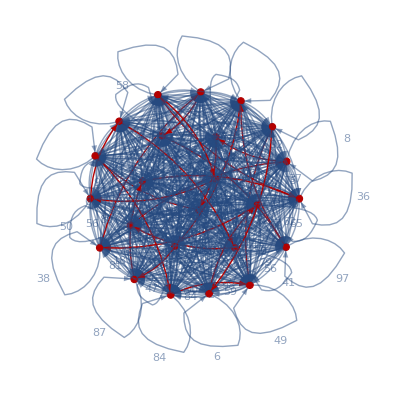

Rule::argrx: Rule called with 3 arguments; 2 arguments are expected.

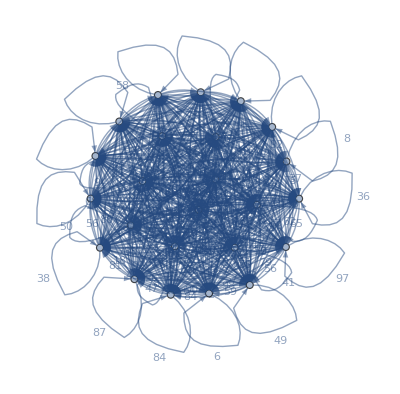

```mathematica
n=24;d=RandomInteger[{1,100},{n,n}];{len,tour}=FindShortestTour[Range[n],DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[n-1]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

## 草稿

```mathematica
FindShortestTour
```

```mathematica
Graph
```

```mathematica
f[x_]:=x/.{y__,z_,z_,w__}:>{y,z,w}
```

```mathematica
f[Flatten/@(Permutations@Permutations[{1,2,3}])][[1;;10]]
```

{{1,2,3,1,3,2,1,3,2,3,1,3,1,2,3,2,1},{1,2,3,1,3,2,1,3,2,3,1,3,2,1,3,1,2},{1,2,3,1,3,2,1,3,3,1,2,2,3,1,3,2,1},{1,2,3,1,3,2,1,3,3,1,2,3,2,1,2,3,1},{1,2,3,1,3,2,1,3,3,2,1,2,3,1,3,1,2},{1,2,3,1,3,2,1,3,3,2,1,3,1,2,2,3,1},{1,2,3,1,3,2,3,1,2,1,3,3,1,2,3,2,1},{1,2,3,1,3,2,3,1,2,1,3,3,2,1,3,1,2},{1,2,3,1,3,2,3,1,3,1,2,2,1,3,3,2,1},{1,2,3,1,3,2,3,1,3,1,2,3,2,1,2,1,3}}

```mathematica
a={3,4,2,1};
b={1,2,3,4};
```

```mathematica
a={3,4,2,1};
b={4,3,2,1};
```

```mathematica
n=1;While[Take[a,n]!=Take[b,-n],n++]
```

```mathematica
n
```

4

```mathematica
Take[a,2]
```

{1,2}

```mathematica
k
```

```mathematica
Table[{Take[a,n],Take[b,-n]},{n,0,4}]
```

{{{},{}},{{3},{1}},{{3,4},{2,1}},{{3,4,2},{3,2,1}},{{3,4,2,1},{4,3,2,1}}}

```mathematica
Table[{Take[a,n]!=Take[b,-n]},{n,1,4}]
```

{{True},{True},{True},{True}}

```mathematica
Block
```

```mathematica
ToString/@Range[len]
```

{1,2,3,4,5}

```mathematica
dis["12345","45213"]
```

3

```mathematica
dis@@@Partition[s1]
```

```mathematica
dis
```

```mathematica
MapThread
```

```mathematica
Thread
```

```mathematica
Map
```

```mathematica
dis[st[[1]],st[[2]]]
```

1

```mathematica
shortestlist=per[[(%255)[[2]]]];
```

```mathematica
(%255)[[2]]//Length
```

721

```mathematica
n
```

4

```mathematica
ToString
```

```mathematica
ToExpression@Characters["1234"]
```

{1,2,3,4}

```mathematica
dis[a_,b_]:=Block[{n=1,x,y},While[Take[a,n]!=Take[b,-n]&&n<len,n++];n]
```

```mathematica
ToExpression[Characters@"1243"]
```

{1,2,4,3}

```mathematica
dis[{1,2,3,4},{1,2,4,3}]
```

ToExpression::notstrbox: Characters[1] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: Characters[2] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

ToExpression::notstrbox: Characters[3] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression::notstrbox will be suppressed during this calculation.

1

```mathematica
dis["1234","2341"]
```

1

```mathematica
Table[dis[per[[i]],per[[i+1]]],{i,1,3!-1}]//Total
```

12

```mathematica
dis["1234","3421"]
```

3

```mathematica
n
```

4

```mathematica
dis[b,a]
```

4

```mathematica
n
```

5

```mathematica
d=SparseArray[{{1,2}->1,{2,1}->1,{6,1}->1,{6,2}->1,{5,1}->1,{1,5}->1,{2,6}->1,{2,3}->10,{3,2}->10,{3,5}->1,{5,3}->1,{3,4}->1,{4,3}->1,{4,5}->15,{4,1}->1,{5,4}->15,{5,2}->1,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity];
```

```mathematica
d//MatrixForm
```

(∞ | 1 | ∞ | 1 | 1 | 1
1 | ∞ | 10 | ∞ | 1 | 1
∞ | 10 | ∞ | 1 | 1 | ∞
1 | ∞ | 1 | ∞ | 15 | ∞
1 | 1 | 1 | 15 | ∞ | ∞
1 | 1 | ∞ | ∞ | ∞ | ∞)

```mathematica
{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(dm[[#1,#2]]&)]
```

{12,{1,6,2,3,5,4,1}}

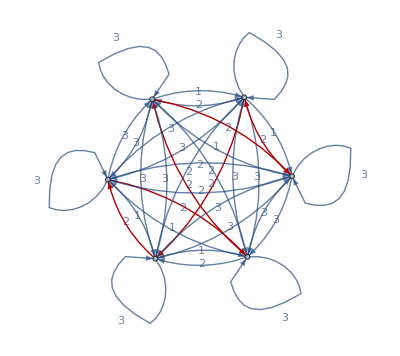

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"],{1->6,6->2,2->3,3->5,5->4,4->1}]
```

```mathematica
dm=Table[dis[per[[i]],per[[j]]],{i,len!},{j,len!}];
```

```mathematica
dm//MatrixForm
```

(4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 1 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 2 | 2 | 4 | 4
4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 1 | 4 | 4
4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1
4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 2 | 2
4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 2 | 2 | 4 | 4 | 4 | 4
4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 1 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4
4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
4 | 4 | 4 | 4 | 1 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4
4 | 4 | 4 | 4 | 2 | 2 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4
2 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4
1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 1 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
4 | 4 | 2 | 2 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 4 | 4 | 1 | 4 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
2 | 2 | 4 | 4 | 4 | 4 | 3 | 3 | 3 | 3 | 3 | 3 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4
3 | 3 | 3 | 3 | 3 | 3 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 1 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4)

```mathematica
FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)]
st=per[[Drop[%[[2]],-1]]](*一种等效的写法*)
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

{1234,3421,1342,4213,3142,2314,1423,4231,3214,1432,4321,2143,4312,1243,2431,3124,2134,3412,4123,3241,1324,2413,4132,2341}

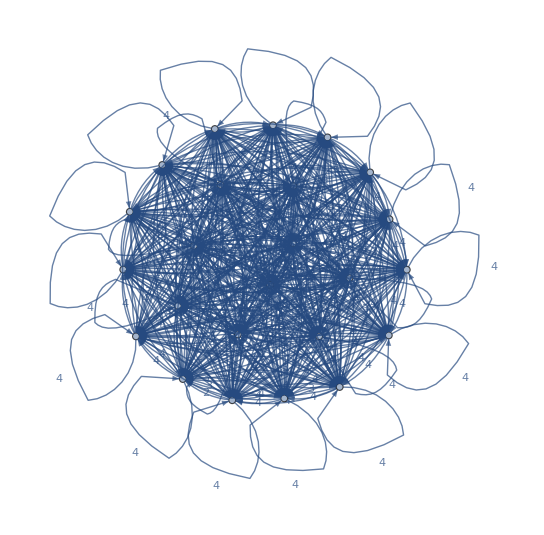

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight",VertexLabels->"Name"]
```

{105,{1,6,2,5,3,4,1}}

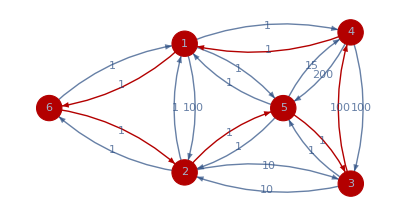

```mathematica
d=SparseArray[{{1,2}->100,{2,1}->1,{6,1}->1,{6,2}->1,{5,1}->1,{1,5}->1,{2,6}->1,{2,3}->10,{3,2}->10,{3,5}->1,{5,3}->1,{3,4}->100,{4,3}->100,{4,5}->200,{4,1}->1,{5,4}->15,{5,2}->1,{1,4}->1,{2,5}->1,{1,6}->1},{6,6},Infinity];{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(d[[#1,#2]]&)]
HighlightGraph[WeightedAdjacencyGraph[d,EdgeLabels->"EdgeWeight",VertexSize-> .25,VertexLabels->Placed[Automatic,Center]],Graph[Rule@@@Partition[tour,2,1]]]
```

```mathematica
Partition[per[[tour]],2,1]
```

{{1234,3421},{3421,1342},{1342,4213},{4213,3142},{3142,2314},{2314,1423},{1423,4231},{4231,3214},{3214,1432},{1432,4321},{4321,2143},{2143,4312},{4312,1243},{1243,2431},{2431,3124},{3124,2134},{2134,3412},{3412,4123},{4123,3241},{3241,1324},{1324,2413},{2413,4132},{4132,2341},{2341,1234}}

```mathematica
dis@@@Partition[per[[tour]],2,1]
```

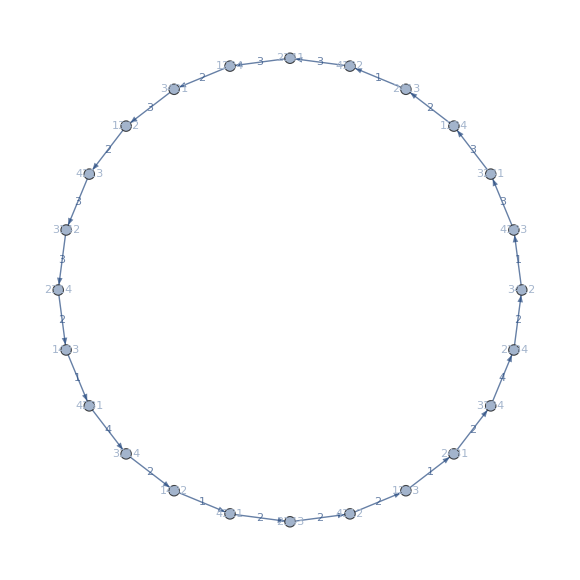

```mathematica
Graph[Rule@@@Partition[per[[tour]],2,1],EdgeLabels->Thread[Rule@@@Partition[per[[tour]],2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexLabels->Placed["Name",Center]]
```

```mathematica
Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]
```

{1→Placed[1234,Center],18→Placed[3421,Center],4→Placed[1342,Center],21→Placed[4213,Center],14→Placed[3142,Center],9→Placed[2314,Center],5→Placed[1423,Center],22→Placed[4231,Center],15→Placed[3214,Center],6→Placed[1432,Center],24→Placed[4321,Center],8→Placed[2143,Center],23→Placed[4312,Center],2→Placed[1243,Center],12→Placed[2431,Center],13→Placed[3124,Center],7→Placed[2134,Center],17→Placed[3412,Center],19→Placed[4123,Center],16→Placed[3241,Center],3→Placed[1324,Center],11→Placed[2413,Center],20→Placed[4132,Center],10→Placed[2341,Center]}

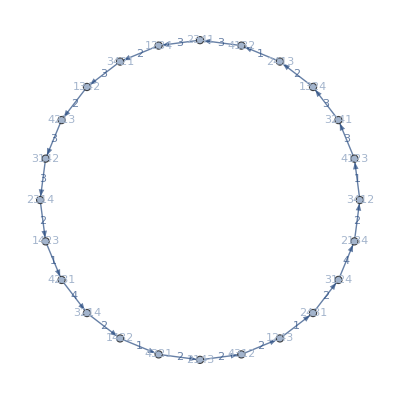

```mathematica
Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]]
```

{54,{1,18,4,21,14,9,5,22,15,6,24,8,23,2,12,13,7,17,19,16,3,11,20,10,1}}

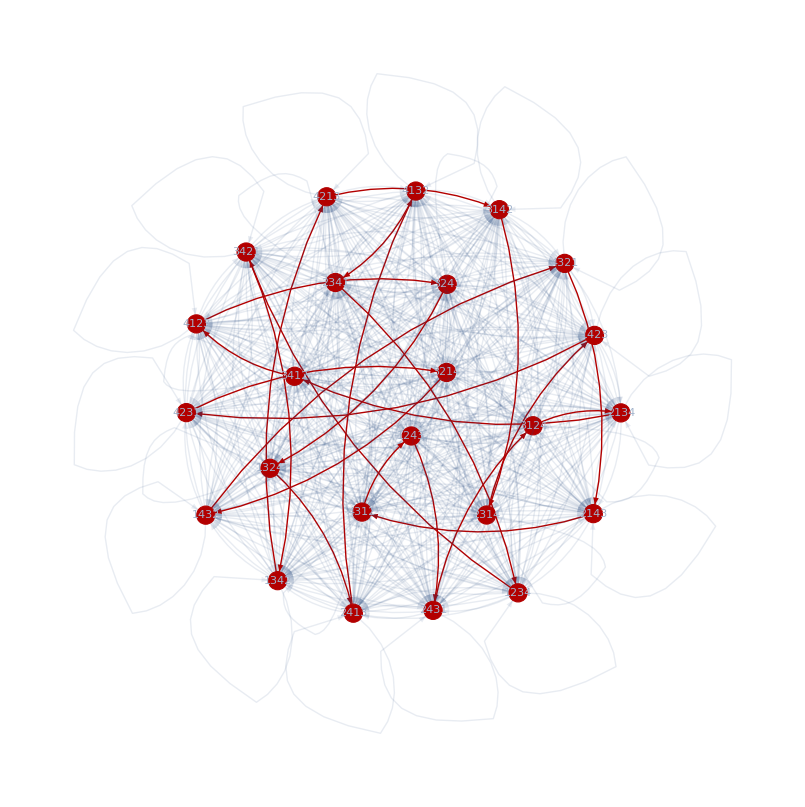

```mathematica
WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]
```

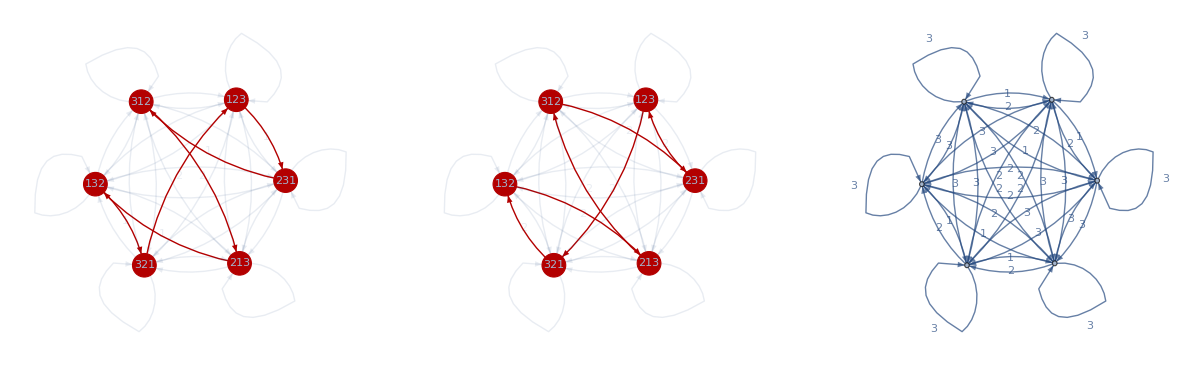

```mathematica
stour3=Flatten@(Position[per,#]&/@(s1~Join~{"123"}))
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]],VertexSize-> .25,VertexLabels->Table[stour3[[i]]->Placed[per[[stour3]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[stour3,2,1],EdgeLabels->Thread[Rule@@@Partition[stour3,2,1]->
dis@@@Partition[per[[stour3]],2,1]]]],
HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

```mathematica
s1~Join~{"123"}
```

{123,231,312,213,132,321,123}

{1,4,5,3,2,6,1}

```mathematica
tour
```

{1,6,2,3,5,4,1}

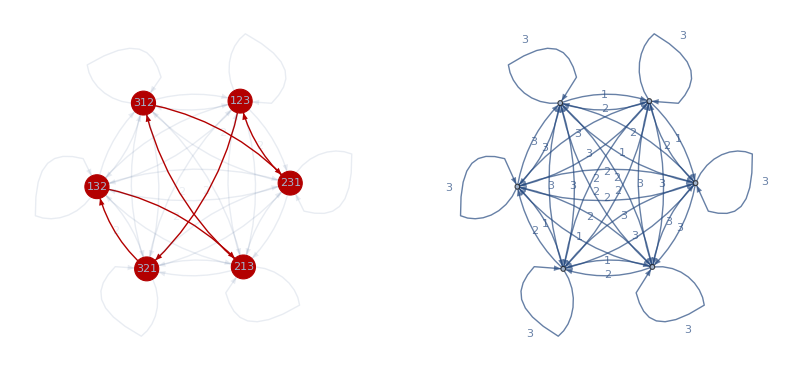

```mathematica
{slen,tour}=FindShortestTour[Range[len!],DistanceFunction->(dm[[#1,#2]]&)];(*等价写法*)
GraphicsRow[{HighlightGraph[WeightedAdjacencyGraph[dm,EdgeStyle->Opacity[0.1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]],VertexSize-> .25,VertexLabels->Table[tour[[i]]->Placed[per[[tour]][[i]],Center],{i,len!}]],Graph[Rule@@@Partition[tour,2,1],EdgeLabels->Thread[Rule@@@Partition[tour,2,1]->
dis@@@Partition[per[[tour]],2,1]]]],WeightedAdjacencyGraph[dm,EdgeLabels->"EdgeWeight"]}]
```

```mathematica
d=RandomInteger[{1,10},{6,6}];
```

{30,{1,6,5,2,4,3,1}}

{12,{1,3,2,5,6,4,1}}

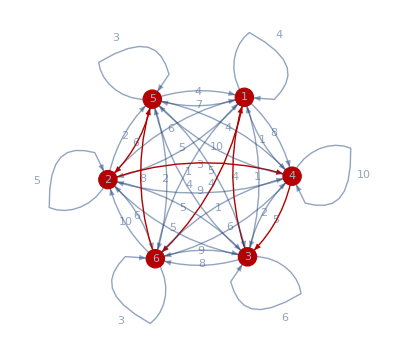

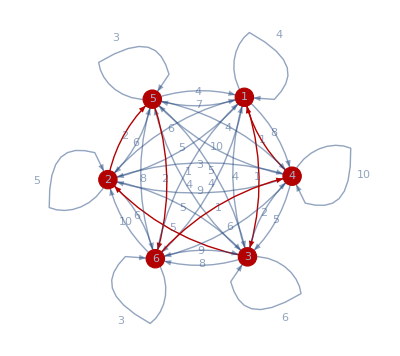

```mathematica
{len,tour}=FindShortestTour[{1,2,3,4,5,6},DistanceFunction->(d[[#1,#2]]&)]
pathls=(({1}~Join~#~Join~{1}&/@(Permutations[Range[5]]+1)));
exp=Partition[#,2,1]&/@pathls;
Apply[d[[#1,#2]]&,exp,{2}];
lengthls=Total/@%;
{len1,tour1}={Min[lengthls],
pathls[[Position[lengthls,Min[lengthls]][[1,1]]]]}
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour,2,1]]]
HighlightGraph[WeightedAdjacencyGraph[d, EdgeLabels->"EdgeWeight",EdgeStyle->Opacity[0.5],VertexSize->0.2,VertexLabels->Placed["Name",Center]],Graph[Rule@@@Partition[tour1,2,1]]]
```

```mathematica
d[[#1,#2]]&@@@Partition[{1,3,2,5,6,4,1},2,1]
```

{1,5,2,2,1,1}

```mathematica
Total[%]
```

12

```mathematica
{4,9,5,2,4,1}
```

{4,9,5,2,4,1}

```mathematica
{{5,5,2,10,2,1},{5,5,2,6,8,4},{5,5,4,4,6,1},{5,5,4,2,1,1},{5,5,8,1,10,4},{5,5,8,8,4,1},{5,3,5,4,2,1},{5,3,5,8,8,4},{5,3,10,5,8,1},{5,3,10,2,9,4},{5,3,6,9,4,4},{5,3,6,8,5,4},{5,2,5,2,6,1},{5,2,5,8,1,1},{5,2,4,5,8,1},{5,2,4,6,9,4},{5,2,2,9,2,1},{5,2,2,1,5,4},{5,6,9,2,10,4},{5,6,9,4,4,1},{5,6,1,5,4,4},{5,6,1,10,5,4},{5,6,8,5,2,1},{5,6,8,4,5,4},{1,5,3,10,2,1},{1,5,3,6,8,4},{1,5,2,4,6,1},{1,5,2,2,1,1},{1,5,6,1,10,4},{1,5,6,8,4,1},{1,2,9,2,2,1},{1,2,9,6,8,4},{1,2,10,6,6,1},{1,2,10,2,10,6},{1,2,6,10,2,4},{1,2,6,8,6,6},{1,4,6,3,6,1},{1,4,6,6,1,1},{1,4,4,9,6,1},{1,4,4,6,10,6},{1,4,2,10,3,1},{1,4,2,1,9,6},{1,8,10,3,10,4},{1,8,10,2,4,1},{1,8,1,9,2,4},{1,8,1,10,6,6},{1,8,8,6,3,1},{1,8,8,4,9,6},{8,9,5,4,2,1},{8,9,5,8,8,4},{8,9,2,5,8,1},{8,9,2,2,9,4},{8,9,6,9,4,4},{8,9,6,8,5,4},{8,5,5,2,2,1},{8,5,5,6,8,4},{8,5,4,6,6,1},{8,5,4,2,10,6},{8,5,8,10,2,4},{8,5,8,8,6,6},{8,10,6,5,8,1},{8,10,6,6,9,4},{8,10,5,5,6,1},{8,10,5,8,10,6},{8,10,2,10,5,4},{8,10,2,9,5,6},{8,6,10,5,4,4},{8,6,10,2,5,4},{8,6,9,5,2,4},{8,6,9,4,6,6},{8,6,8,6,5,4},{8,6,8,5,5,6},{7,6,5,2,6,1},{7,6,5,8,1,1},{7,6,3,5,8,1},{7,6,3,6,9,4},{7,6,6,9,2,1},{7,6,6,1,5,4},{7,5,5,3,6,1},{7,5,5,6,1,1},{7,5,2,9,6,1},{7,5,2,6,10,6},{7,5,8,10,3,1},{7,5,8,1,9,6},{7,4,9,5,8,1},{7,4,9,6,9,4},{7,4,5,5,6,1},{7,4,5,8,10,6},{7,4,6,10,5,4},{7,4,6,9,5,6},{7,2,10,5,2,1},{7,2,10,3,5,4},{7,2,9,5,3,1},{7,2,9,2,9,6},{7,2,1,9,5,4},{7,2,1,5,5,6},{4,10,5,2,10,4},{4,10,5,4,4,1},{4,10,3,5,4,4},{4,10,3,10,5,4},{4,10,2,5,2,1},{4,10,2,4,5,4},{4,9,5,3,10,4},{4,9,5,2,4,1},{4,9,2,9,2,4},{4,9,2,10,6,6},{4,9,4,6,3,1},{4,9,4,4,9,6},{4,1,9,5,4,4},{4,1,9,2,5,4},{4,1,5,5,2,4},{4,1,5,4,6,6},{4,1,10,6,5,4},{4,1,10,5,5,6},{4,8,6,5,2,1},{4,8,6,3,5,4},{4,8,5,5,3,1},{4,8,5,2,9,6},{4,8,4,9,5,4},{4,8,4,5,5,6}}[[104]]
```

{4,9,5,2,4,1}

```mathematica
d[[6,3]]
```

10

```mathematica
d[[#1,#2]]&@@@(exp[[1]])
```

{2,7,10,10,9,10}

```mathematica
Min[lengthlist]
```

22

```mathematica
Position[pathls,{1,2,3,5,6,4,1}]
```

{{4}}

```mathematica
Position[lengthlist,Min[lengthlist]]
```

{{104}}

```mathematica
pathls[[71]]
```

{1,4,6,5,2,3,1}